### A little horizon calculator

How far do you have to walk before your friend disappears?

```mathematica
radius= 40000000/(2Pi); (*approximate radius of the earth, in meters*)
height = 2; (*our heights, rounded, in meters*)
horizon  = √((radius+height)^2-radius^2);(*how far to the horizon*)
walk = 2horizon//N (* the distance, in meters, to walk*)
```

10092.5

More generally, if you are viewerheight tall,  how far away must an object objectheight be to disappear?

```mathematica
disappear[ viewerheight_:2,objectheight_:2,radius_: 40000000/(2Pi)]:=
 Plus@@(√((radius+#)^2-radius^2)&/@{viewerheight,objectheight})
```

```mathematica
disappearHeightinFeetFarInMiles [viewerheight_:6,objectheight_:6,radius_: 4000]:=
disappear[viewerheight*12*2.54/100,objectheight*12*2.54/100,radius*5280*12*2.54/100]*100/2.54/12/5280
```

Conversely, given a distance away, how much can be hidden?

```mathematica
howhigh[viewerheight_:2,distance_:10000, radius_: 40000000/(2Pi)]:=-radius+√(viewerheight^2+distance^2+2 viewerheight radius+radius^2-2 distance √(viewerheight (viewerheight+2 radius)))
```

```mathematica
howhighinFeetFarInMiles[viewerheight_:2,distance_:10000]:=
howhigh[viewerheight*12*2.54/100,distance*5280*12*2.54/100]100/2.54/12
```

#### examples

```mathematica
disappear[2,50.]/1000/1.6
```

```mathematica
howhighinFeetFarInMiles[6,12]
```

54.0769

```mathematica
disappear[2,50.]/1000/1.6
```

```mathematica
disappear[2,0.]
```

3.07822

```mathematica
disappearHeightinFeetFarInMiles[6,10]
```

6.90761

```mathematica
disappearHeightinFeetFarInMiles[0,0]
```

0.

This plot is quadratic, so always looks like this, with the horizon disappearing the fastest as we first blast off.  Asympotically, it is just the distance to the earth itself.

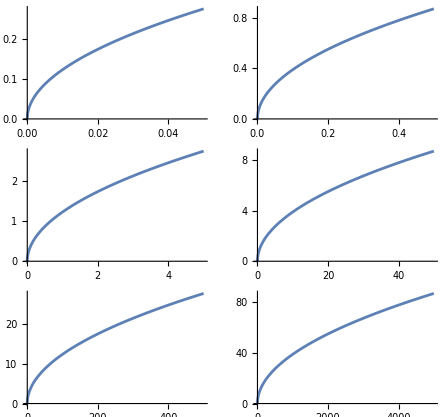

```mathematica
GraphicsGrid@Table[Table[Plot[disappearHeightinFeetFarInMiles[x,0],{x,0,r}], {r, {{.05,.5},{5, 50},{ 500,5000},{ 50000, 500000}}[[i]]}], {i, 3}]
```